```mathematica
Clear["Global`*"]
```

```mathematica
k=1.0; a=0.05;
```

```mathematica
solve[ic_]:=(
Dsys={x'[t]==v[t], v'[t] + k x[t] (1 + Exp[-x[t]/a]) == 0,
x[0]==ic, v[0]==0};
sols=NDSolve[Dsys,{v[t],x[t]},{t,0,10}];
Return[sols];
)
```

```mathematica
solve[1]
```

{{v[t]→InterpolatingFunction[{{0., 10.}}, <>][t],x[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

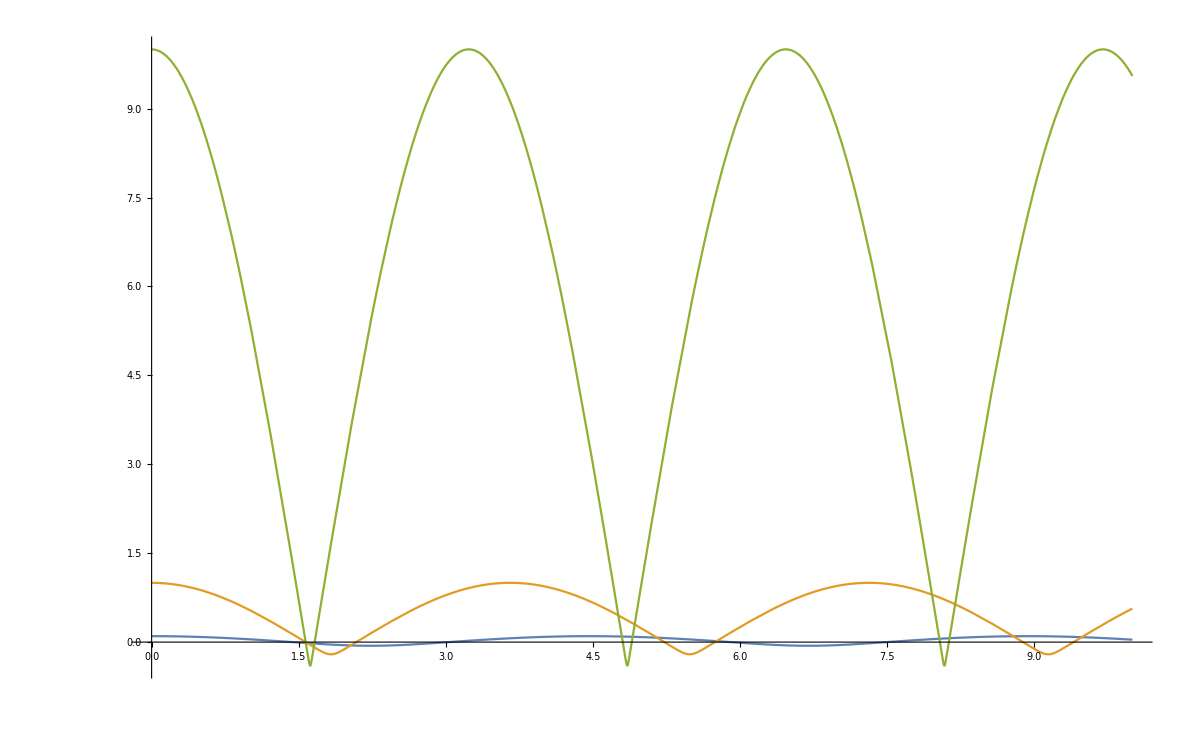

```mathematica
Plot[{Evaluate[x[t]/.solve[0.1]], Evaluate[x[t]/.solve[1]], Evaluate[x[t]/.solve[10]]}, {t, 0, 10}]
```